```mathematica
Quit[];
```

12290

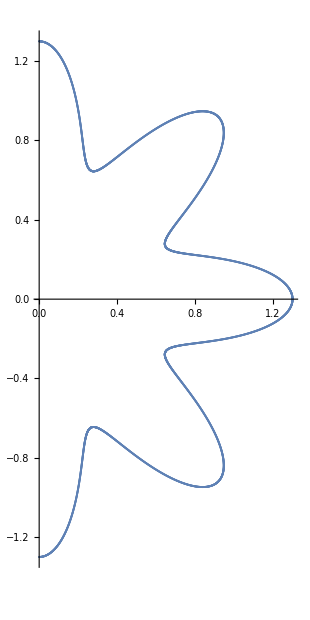

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["test.txt","Table"];
cx=data⟦1;;(Length@data+1)/3⟧;
cy=data⟦(Length@data+1)/3+1;;(Length@data+1)/3*2⟧;
h=data⟦(Length@data+1)2/3+1;;-1⟧;
Length@data
Subscript[sx, i_][t_]:=cx⟦i,1⟧+cx⟦i,2⟧t+(cx⟦i,3⟧t^2+cx⟦i,4⟧t^3+cx⟦i,5⟧t^4+cx⟦i,6⟧t^5)
Subscript[sy, i_][t_]:=cy⟦i,1⟧+cy⟦i,2⟧t+(cy⟦i,3⟧t^2+cy⟦i,4⟧t^3+cy⟦i,5⟧t^4+cy⟦i,6⟧t^5)


{x[t_],y[t_]}=(1+0.2Cos[8t]){Sin[t],Cos[t]};
Table[{Subscript[sx, i][t],Subscript[sy, i][t]},{i,1,Length@cx-1}];
Show[
ListPlot[Transpose[{cx⟦All,1⟧,cy⟦All,1⟧}]]
(*,ParametricPlot[p[θ],{θ,0,π},PlotStyle->Red]*)
(*ParametricPlot[{%⟦1;;10;;2⟧,%⟦2;;11;;2⟧},{t,0,1},AspectRatio->Automatic]*)
,AspectRatio->Automatic,ImageSize->Medium]
(*Table[{t+i,Subscript[sy, i]''''[t]/h⟦i⟧^4},{i,1,Length@cx-1}];
Show[
ParametricPlot[{%⟦1;;-1;;2⟧,%⟦2;;-1;;2⟧},{t,0,1},AspectRatio->Automatic]
,AspectRatio->0.5]*)
```

```mathematica
(p[t])⟦1⟧
```

(1+0.2 Cos[8 t]) Sin[t]

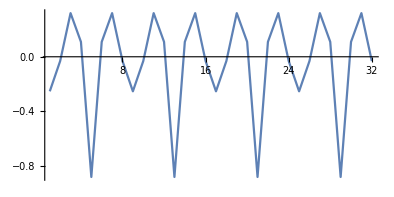

```mathematica
Clear[i,kv,kvt]
θ=Table[ArcCos[Subscript[sy, i][0]/√((Subscript[sx, i][0])^2+ (Subscript[sy, i][0])^2)],{i,1,Length@cx}];
Subscript[kv, i_][t_]:=(Subscript[sx, i]'[t]Subscript[sy, i]''[t]-Subscript[sy, i]'[t]Subscript[sx, i]''[t])/((Subscript[sx, i]'[t])^2+(Subscript[sy, i]'[t])^2)^1.5
kvt[t_]:=(x'[t]y''[t]-y'[t]x''[t])/(x'[t]^2+y'[t]^2)^1.5
Table[Subscript[kv, i][0]-kvt[θ⟦i⟧],{i,1,Length@cx -1}];
Show[
ListPlot[%,PlotRange->All,Joined->True],AspectRatio->0.5,PlotRange->All]
```

```mathematica
6.219718254214801*^-7
```

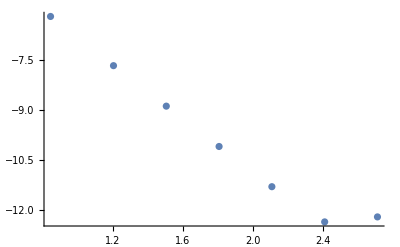

FittedModel[-3.59043-3.462 x]

```mathematica
dd={{7,6.219718254214801*^-7},
{16,2.1043927281305663*^-8},
{32,1.2964614815730302*^-9},
{64,8.074397574164838*^-11},
{128,5.0717728627969194*^-12},
{256,4.4955358879938956*^-13},
{512,6.340639818747107*^-13}
};
ListPlot@Log10@dd
LinearModelFit[Log10@dd,{x},x]
```